# Primer Intento

```mathematica
Data=Import["C:\\Users\\Administrador\\Downloads\\RESULTS-VIDEOS-RelevantesxGumelab2023-10-17 15_25_04.395709.xlsx"];
```

Import::somedata: Some data could not be imported as XLSX.

```mathematica
Position[Flatten[Data[[All,1]]],"hashtagsTituloVideo"][[1,1]]
```

6

```mathematica
NewData=Data[[1]][[All,{6,24}]];
```

```mathematica
Reverse[SortBy[Tally[NewData[[All,1]][[2;;]]],Last]]
```

{{[],3279},{['#LosCompadritos'],33},{['#MineríaConPropósito'],31},{['#HistoriasEnMovimiento'],14},{['#HablandoSeEntiendeLaGente4P0'],14},{['#HablandoSeEntiendeLaGente'],14},{['#EnVivo'],10},{['#TodosCabemos'],5},{['#HablandoSeEntiendeLaGente4'],5},{['#DemoDay'],5},{['#SOSRealJaenCF'],4},{['#Minería4P0'],4},{['#Minería4'],4},{['#JericóCircular'],4},{['#AudienciaPúblicaAmbiental'],4},{['#shorts'],3},{['#Minería'],3},{['#JuntosConstruimosFuturo'],3},{['#HistoriasDeVida'],3},{['#HablemosdeQuebradona'],3},{['#EnVideo', '#LaNoticia'],3},{['#CumpliendoSueños'],3},{['#CreemosEnPanamá'],3},{['#Covid19'],3},{['#AEstaHora', '#EnVivo'],3},{['#8514'],3},{['#UnPropósitoPorLaVida'],2},{['#SotoNorte'],2},{['#SiSePuede'],2},{['#SeguridadMinera'],2},{['#SalvemosAlSuroeste'],2},{['#QuédateEnCasa'],2},{['#ProJericó'],2},{['#NoticiaDestacada'],2},{['#MineriaViva'],2},{['#MineradeCobreQuebradona'],2},{['#MejorConArgumentos'],2},{['#loscompadritos'],2},{['#LoQueNosUne'],2},{['#LeyDeMinería'],2},{['#JuntosConstruimosEmpresa'],2},{['#JericóCompraJericó'],2},{['#HablandoSeEntiendeLaGente4P0', '#EnVivo', '#MineríaConPropósito'],2},{['#EnVivo', '#NoTeLoPierdas'],2},{['#EnVivo', '#AEstaHora', '#Minería4P0'],2},{['#EconomíaCircular', '#MineríaConPropósito'],2},{['#Conéctate', '#EnVivo'],2},{['#ComunicamosConTransparencia'],2},{['#AntioquiaMásViva'],2},{['#8465'],2},{['#3'],2},{['#2'],2},{,2},{['#Yumbo'],1},{['#YoCreoEnQuebradona'],1},{['#yeso', '#albañiles', '#perlita', '#professional', '#reformasdecasas'],1},{['#viral'],1},{['#VerdaderaMinería'],1},{['#Usac'],1},{['#Urten60'],1},{['#UnidosSomosMás'],1},{['#UNIDOSConElGobernador'],1},{['#TodoPorCalifornia', '#ANLA'],1},{['#TierraDeTalentos'],1},{['#TICSO2022'],1},{['#TíaMaría'],1},{['#TardesEnFamiia'],1},{['#Tarapacá'],1},{['#TamboQuemado'],1},{['#TalentoJericoano'],1},{['#SUROESTENOTICIAS'],1},{['#stopsiluro'],1},{['#sosrecre'],1},{['#SomosMocoa'],1},{['#SMGE'],1},{['#siempreadelante', '#medellin'],1},{['#Shorts', '#Fluorita'],1},{['#shorts', '#ecuador', '#independientedelvalle'],1},{['#shorts', '#ecuador', '#adn'],1},{['#Shorts'],1},{['#SeñalParaPensar'],1},{['#Sembratón'],1},{['#SantaMisa'],1},{['#santa', '#hermandad', '#recreaciónhistórica', '#recreacion', '#12deoctubre'],1},{['#SAF'],1},{['#roça', '#colono', '#extensãorural', '#agro', '#pecuaria', '#campo', '#rural'],1},{['#RetosDeLaMinería'],1},{['#retoindustrialniu'],1},{['#ReportajesTA', '#minería', '#BajoCauca'],1},{['#Renovar', '#Floridablanca'],1},{['#ReactivaciónSostenible'],1},{['#RadioOnline'],1},{['#QuebradonaDeCorazón'],1},{['#pt', '#parobe', '#comunicação'],1},{['#propiedadraizmedellin'],1},{['#pozosdeagua', '#chile', '#pozo', '#maquinaperforadora'],1},{['#policianacional', '#todos', '#ecuador', '#chalecos', '#fypシ'],1},{['#Piragua'],1},{['#PiensaEnGrande'],1},{['#peler', '#moringa', '#pelletmill'],1},{['#PEDROPARRA', '#barata'],1},{['#OrgullosamenteMineros'],1},{['#operativo', '#construcción'],1},{['#noticias', '#virall', '#ultimo', '#news', '#esmeraldas'],1},{['#NoticiasQueMerecemos'],1},{['#Noticias', '#ciudad', '#Colombia'],1},{['#NoticiaDeInterés', '#NoticiaPositiva'],1},{['#NoTeLoPierdas', '#HablandoSeEntiendeLaGente4', '#ParqueBiodinámico'],1},{['#NoTeLoPierdas', '#HablandoSeEntiendeLaGente4'],1},{['#NoTeLoPierdas', '#EnVivo'],1},{['#NoTeLoPierdas'],1},{['#NegociosVerdes'],1},{['#NCR'],1},{['#NavidadPorElMundo'],1},{['#MiningWithPurpose'],1},{['#MinesaSolidario'],1},{['#Mineriaviva'],1},{['#MineríaParaElProgreso'],1},{['#mineria', '#explosivo'],1},{['#MineríaConSentido'],1},{['#MineríaConPropósito', '#TodosCabemos'],1},{['#MineríaConPropósito', '#HablandoSeEntiendeLaGente4'],1},{['#Minería4PuntoCero'],1},{['#MiércolesMinero'],1},{['#Mie'],1},{['#MiBiciPostobón'],1},{['#MartesSAI'],1},{['#marcandoruta'],1},{['#LTenVivo'],1},{['#LosCompadritos', '#MineríaEnTuVida'],1},{['#LosCompadritos', '#Jericó'],1},{['#liga1', '#peru'],1},{['#LeyAntibarrabrava', '#RL18'],1},{['#LdN', '#agriCULTURA'],1},{['#LasTunas'],1},{['#Las8TesasDeLaMinería'],1},{['#LaRegiónSeSiente'],1},{['#LaNoticia', '#EnVideo'],1},{['#LaLibertad', '#ARCC'],1},{['#LALIBERTAD'],1},{['#LaGuaduaComoInsipiración'],1},{['#LA_GRANJA'],1},{['#JuevesCultural'],1},{['#Innovabio'],1},{['#independiente', '#futbol', '#viral', '#argentina'],1},{['#IdeasParaCompartir'],1},{['#HéroesDeCobre'],1},{['#helicóptero', '#ibama', '#fiscalização', '#ar'],1},{['#helicóptero'],1},{['#HablandoSeEntiendeLaGenteP0'],1},{['#gulupa', '#cultivo', '#emprendimiento', '#yarumal'],1},{['#GraciasMinerosPor'],1},{['#GeólogosPorUnDía'],1},{['#Garagemejia503'],1},{['#ganadería', '#colombia', '#ranchohumilde', '#amorpropio', '#sueños', '#amor', '#brawlstars'],1},{['#galinhacaipira', '#criacaodegalinhas'],1},{['#FueraAngloGold'],1},{['#FocusNoticias'],1},{['#flashinformativo'],1},{['#FeriadeOportunidades'],1},{['#Expositores'],1},{['#ERTZAINTZA'],1},{['#EnVivo', '#TeEsperamos', '#NoTeLoPierdas', '#QuédateEnCasa'],1},{['#EnVivo', '#MineríaConPropósito'],1},{['#EnVivo', '#HablandoSeEntiendeLaGente4P0'],1},{['#EnVivo', '#HablandoSeEntiendeLaGente'],1},{['#EnVivoAsí', '#MíneríaConPropósito'],1},{['#EnVivo', '#AEstaHora', '#MineríaCónPropósito'],1},{['#EnVivo', '#AEstaHora', '#MineríaConPropósito'],1},{['#EnVideo', '#LaNoticia', '#JuntosConstruimosBienestar'],1},{['#EnEntrevista'],1},{['#EncadenamientoProductivo'],1},{['#ElRemolino'],1},{['#ElOjoDeLaTormenta'],1},{['#Elecciones'],1},{['#ElCineYSusProtagonistas'],1},{['#ELAMI2021'],1},{['#EJERCITO', '#CCTV', '#news', '#noticias'],1},{['#ecuador', '#mineria', '#mineriaecuador'],1},{['#econews'],1},{['#DNEWS'],1},{['#DNews'],1},{['#DíaMundialDeLosAnimales'],1},{['#DíaMundialDelMedioAmbiente', '#DaleUnaManoAlPlaneta'],1},{['#DíaMundialDelAgua'],1},{['#DíaMundiaDelMedioAmbiente'],1},{['#DíaDeMineríaConPropósito'],1},{['#Díadelminero2021'],1},{['#Destacado', '#EnVideo'],1},{['#Conversatorio'],1},{['#constructora', '#koi', '#proyectosdevivienda'],1},{['#construcción', '#grader', '#mantenimiento', '#construcción'],1},{['#construccion', '#bienesraices', '#galero'],1},{['#construção', '#geral'],1},{['#ConsejoTA'],1},{['#Conéctate', '#NoTeLoPuedesPerder'],1},{['#Conéctate', '#EnVivo', '#MineríaConPropósito', '#HablandoSeEntiendeLaGente4'],1},{['#Conéctate'],1},{['#concejodemedellín'],1},{['#CNZKING', '#bomba', '#bombeo', '#lodos', '#carbón', '#minas', '#minería', '#industrial', '#slurrypump', '#dragado', '#relaves'],1},{['#citaçõesbíblicas', '#adoração', '#reflexão'],1},{['#canijr258'],1},{['#bukele', '#asamblea'],1},{['#brasileirão', '#libertadores', '#futebol', '#amigos'],1},{['#botswana'],1},{['#BosquesdeVida'],1},{['#borada', '#ceramica', '#juntas', '#acabadosdeconstrucción', '#shorts'],1},{['#Bandoneonísimo'],1},{['#Atención', '#EnVivo'],1},{['#ATENCIÓN'],1},{['#Atención'],1},{['#AsociacionDeBeticos'],1},{['#AsambleaDepartamental', '#antioquia', '#medellin', '#discapasidad', '#visual', '#universidad'],1},{['#arquitecturametalica'],1},{['#ÁreaSostenible'],1},{['#AntioquiaMásVida'],1},{['#antioquia', '#DT175'],1},{['#ANIVERSARIOAMSAC'],1},{['#anglogoldapp'],1},{['#AngloGold'],1},{['#anglogold'],1},{['#AloLegal'],1},{['#AlaVentura', '#LAUNIÓ'],1},{['#AgroExporta'],1},{['#agalopetendido', '#chiringas'],1},{['#AEstaHora', '#EnVivo', '#MineríaConPropósito'],1},{['#AEstaHora', '#EnVivo', '#HablandoSeEntiendeLaGente4'],1},{['#ActosYDecisiones'],1},{['#AccionesParaLaPaz'],1},{['#AcciónDemocrática'],1},{['#ABCDeLaRemediación', '#7'],1},{['#90Segundos'],1},{['#530'],1},{['#5'],1},{['#4'],1},{['#1', '#MineríaCircularYSostenible'],1},{['#14'],1},{['#12deoctubre', '#españa', '#desfilemilitar2023', '#recreaciónhistórica'],1},{['#11'],1},{['#1'],1}}

```mathematica
(*{Canales, Hashtags}*)
```

```mathematica
NewData1=DeleteDuplicates[Select[NewData[[2;;]],Unequal[#[[1]],"[]"]&&Unequal[#,{"",""}]&]];
```

```mathematica
NewData1=Table[{Flatten[StringSplit[NewData1[[ii]][[1]],","]],NewData1[[ii]][[2]]},{ii,1,Length[NewData1]}];
```

```mathematica
NewData1=Flatten[Table[{StringReplace[NewData1[[ii,1]][[jj]],{"["->"","]"->""}],NewData1[[ii,2]]},{ii,1,Length[NewData1]},{jj,1,Length[NewData1[[ii,1]]]}],1];
```

```mathematica
StringSplit[NewData1[[1,1]],{"[","]"}]
```

{'#MineradeCobreQuebradona'}

```mathematica
Hashtags=Tally[NewData1[[All,1]]][[All,1]];
Canales=Tally[NewData1[[All,2]]][[All,1]];
```

```mathematica
NewPositions=Table[{Position[Hashtags,NewData1[[ii,1]]][[1,1]],Position[Canales,NewData1[[ii,2]]][[1,1]]+Length[Hashtags]},{ii,1,Length[NewData1]}];
```

```mathematica
Length[Canales]
```

122

```mathematica
Length[Hashtags]
```

239

```mathematica
Select[Hashtags,Not[StringContainsQ[#,"#"]]&]
```

{}

```mathematica
VrtxLabl=Join[Table[Position[Hashtags,NewData1[[ii,1]]][[1,1]]->NewData1[[ii,1]],{ii,1,Length[NewData1]}],Table[Position[Canales,NewData1[[ii,2]]][[1,1]]+Length[Hashtags]->NewData1[[ii,2]],{ii,1,Length[NewData1]}]];
```

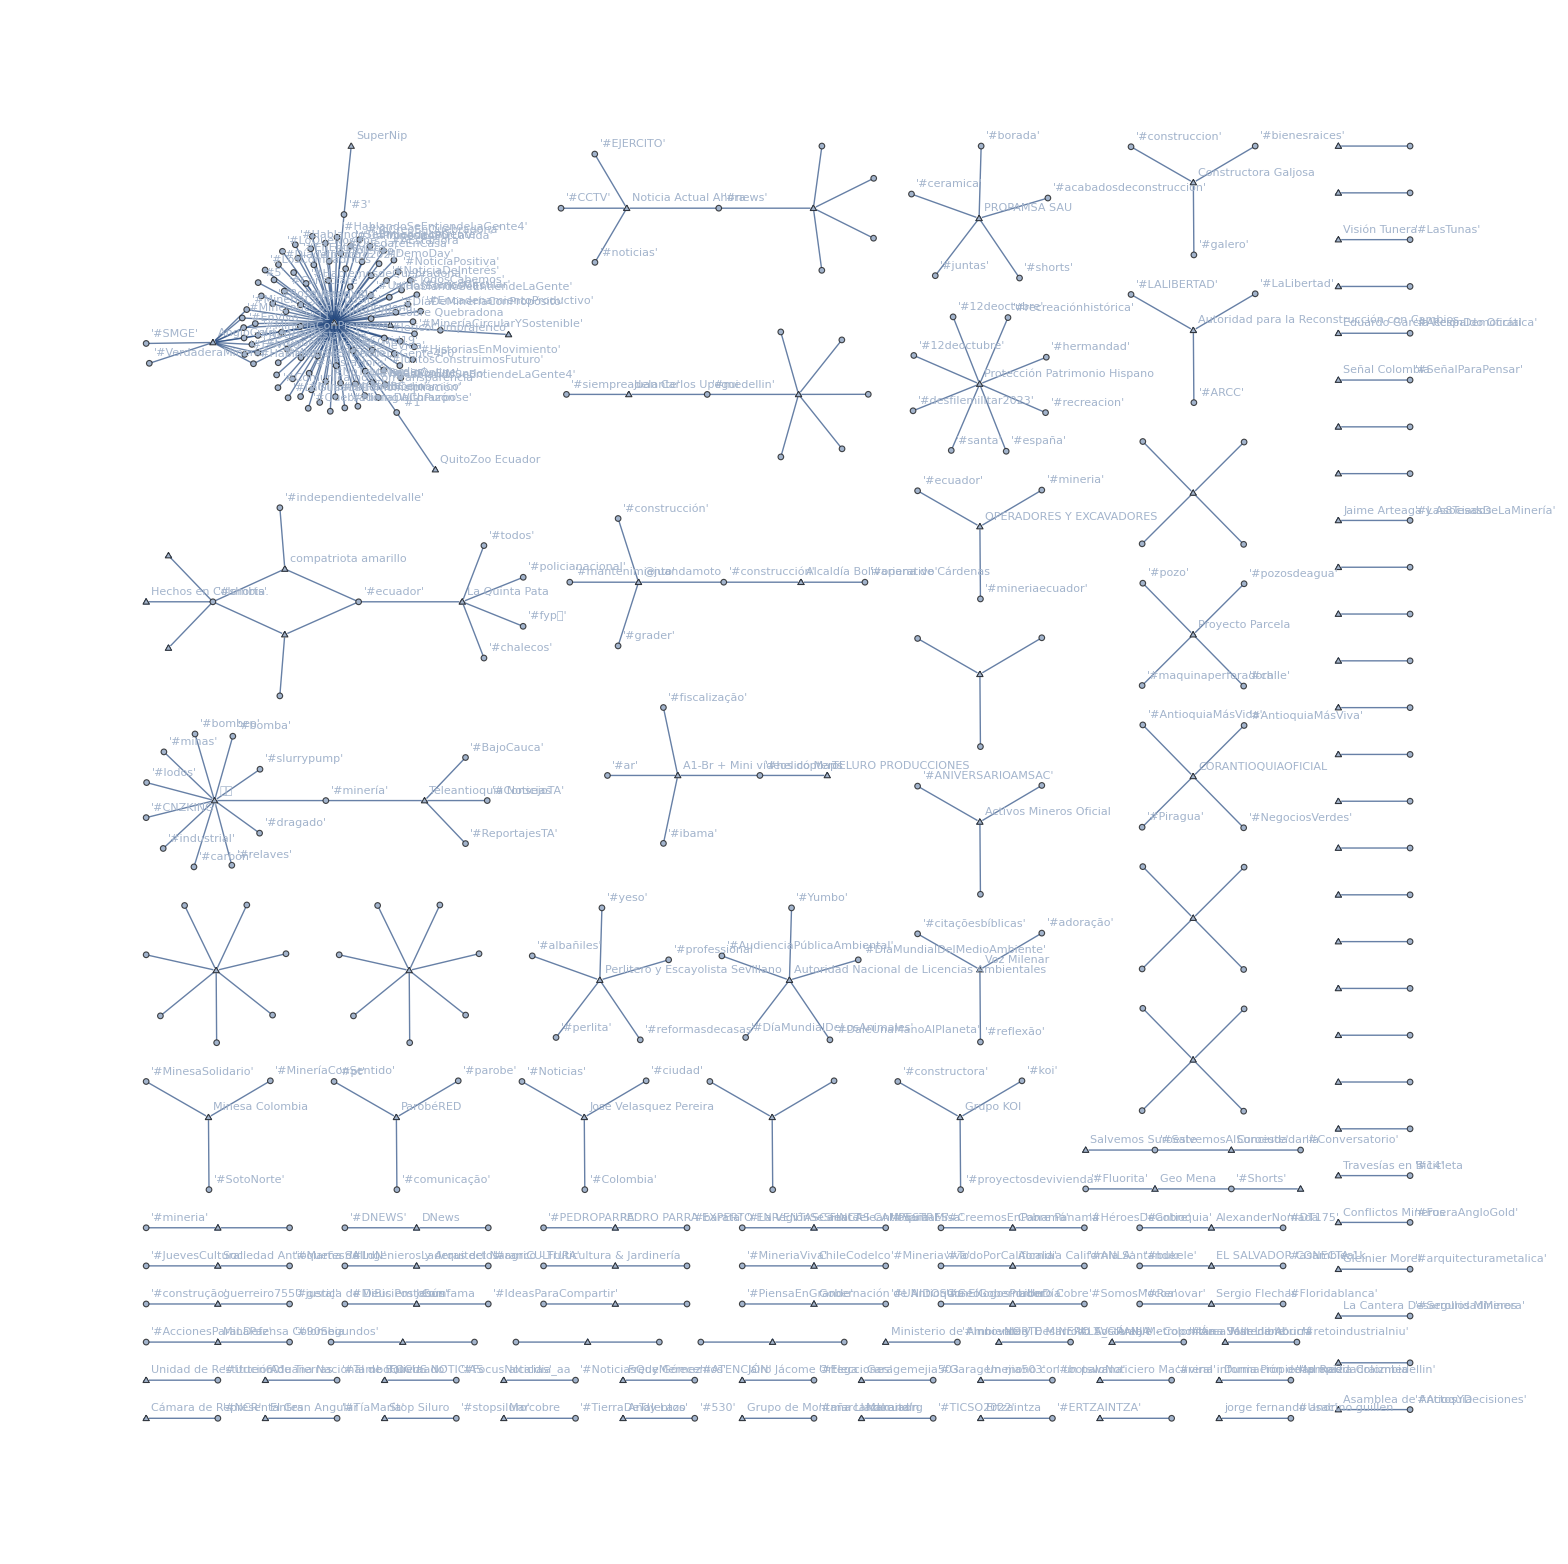

```mathematica
Graph[DeleteDuplicates[Table[NewPositions[[ii,1]]<->NewPositions[[ii,2]],{ii,1,Length[NewPositions]}]],VertexSize->0.6,VertexShapeFunction->Table[If[ii<Length[Hashtags],ii->"Circle",ii->"Triangle"],{ii,1,Length[Canales]+Length[Hashtags]}],VertexLabels->VrtxLabl,ImageSize->3600]
```

```mathematica
SpecialList=DeleteDuplicates[Select[NewPositions,MemberQ[Select[Tally[NewPositions[[All,1]]],#[[2]]>1&][[All,1]],#[[1]]]&]];
```

```mathematica
DeleteDuplicates[Select[VrtxLabl,MemberQ[DeleteDuplicates[Flatten[SpecialList]],#[[1]]]&]]
```

{1→['#MineradeCobreQuebradona'],3→['#MineríaConPropósito'],4→['#NoticiaDestacada'],15→['#HablandoSeEntiendeLaGente4P0', '#EnVivo', '#MineríaConPropósito'],21→['#HablandoSeEntiendeLaGente4P0'],28→['#SalvemosAlSuroeste'],57→['#EconomíaCircular', '#MineríaConPropósito'],72→['#shorts'],77→['#EnVivo'],79→['#3'],174→['#2'],200→['#EnVideo', '#LaNoticia'],239→AngloGold Ashanti,240→Minera de Cobre Quebradona,241→Salvemos Suroeste,247→Conciudadanía,262→Hechos en Colombia.,293→SuperNip,334→FÚTBOL MILENIO,340→Empresa Nicaragüense de Electricidad ENEL,341→Antonio Fernandez Olombrada}

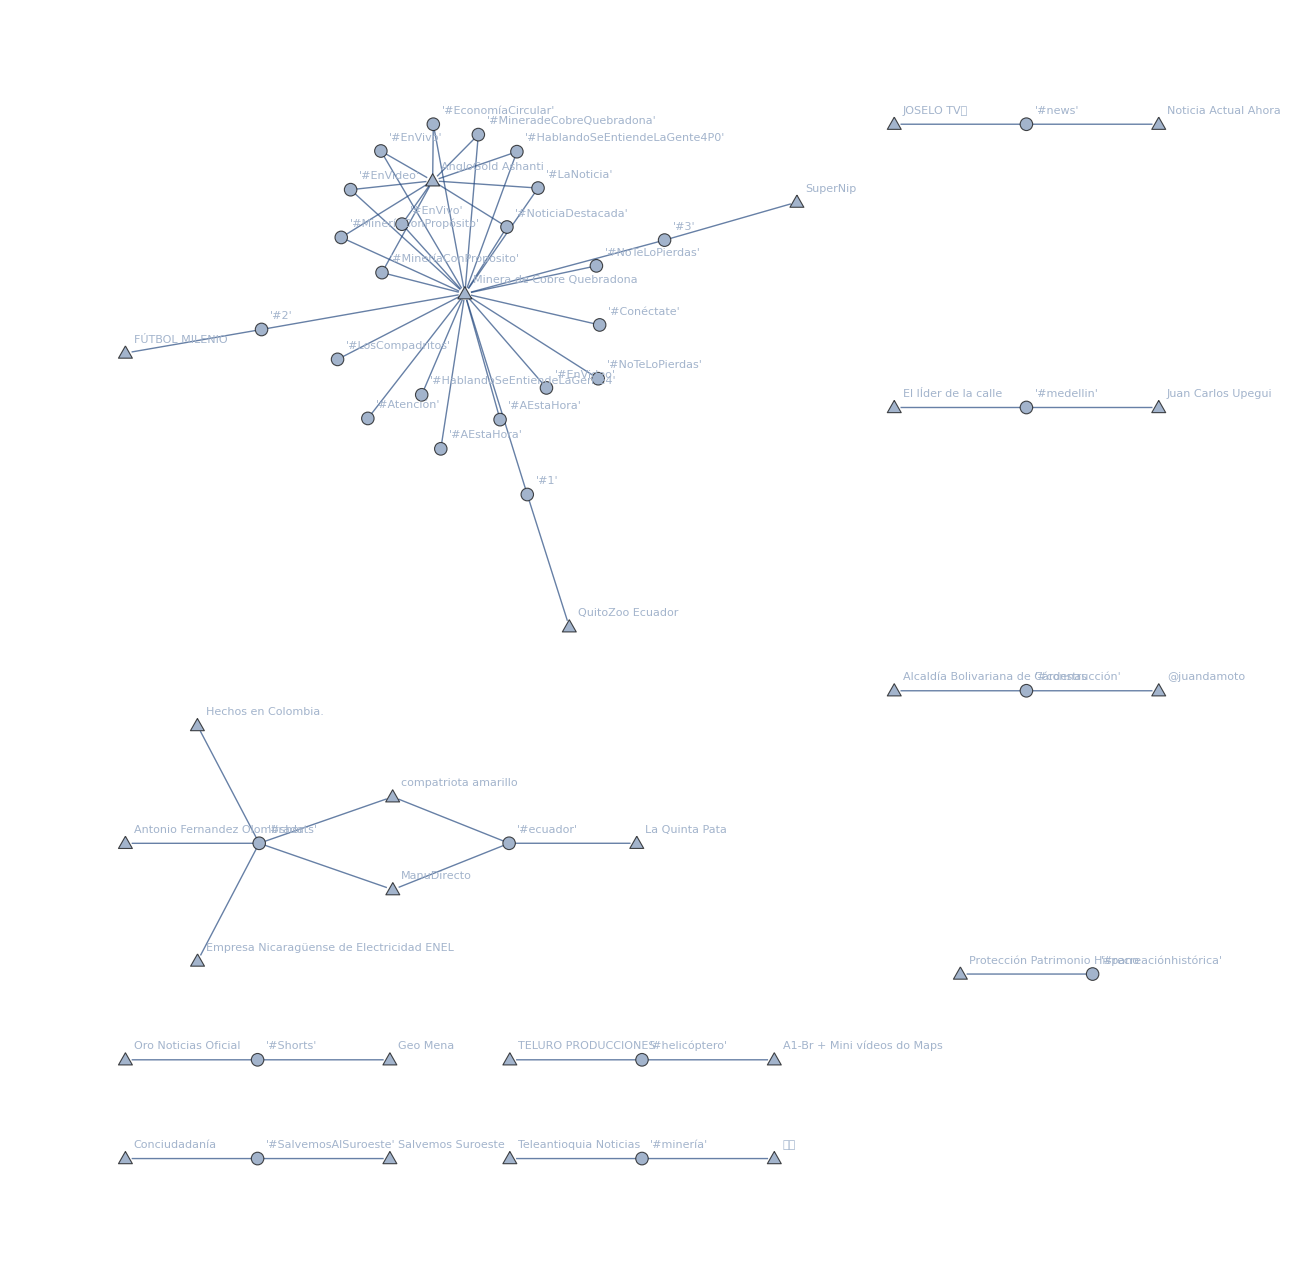

```mathematica
Graph[Table[SpecialList[[ii,1]]<->SpecialList[[ii,2]],{ii,1,Length[SpecialList]}],VertexShapeFunction->Select[Table[If[ii<Length[Hashtags],ii->"Circle",ii->"Triangle"],{ii,1,Length[Canales]+Length[Hashtags]}],MemberQ[DeleteDuplicates[Flatten[SpecialList]],#[[1]]]&],VertexLabels->DeleteDuplicates[Select[VrtxLabl,MemberQ[DeleteDuplicates[Flatten[SpecialList]],#[[1]]]&]],VertexSize->0.3,ImageSize->1300]
```

# Segundo Intento

```mathematica
NewData=Import["C:\\Users\\Administrador\\Downloads\\datos_hashtags.xlsx"][[1]][[All,{2,3}]];
```

```mathematica
NewDataClean=DeleteDuplicates[NewData[[2;;]]];
```

```mathematica
Hashtags=NewDataClean[[All,1]];
Canales=NewDataClean[[All,2]];
```

```mathematica
NewPositions=Table[{Position[Hashtags,NewDataClean[[ii,1]]][[1,1]],Position[Canales,NewDataClean[[ii,2]]][[1,1]]+Length[Hashtags]},{ii,1,Length[NewDataClean]}];
```

```mathematica
VrtxLabl=DeleteDuplicates[Join[Table[Position[Hashtags,NewDataClean[[ii,1]]][[1,1]]->NewDataClean[[ii,1]],{ii,1,Length[NewDataClean]}],Table[Position[Canales,NewDataClean[[ii,2]]][[1,1]]+Length[Hashtags]->NewDataClean[[ii,2]],{ii,1,Length[NewDataClean]}]]];
```

## Graph

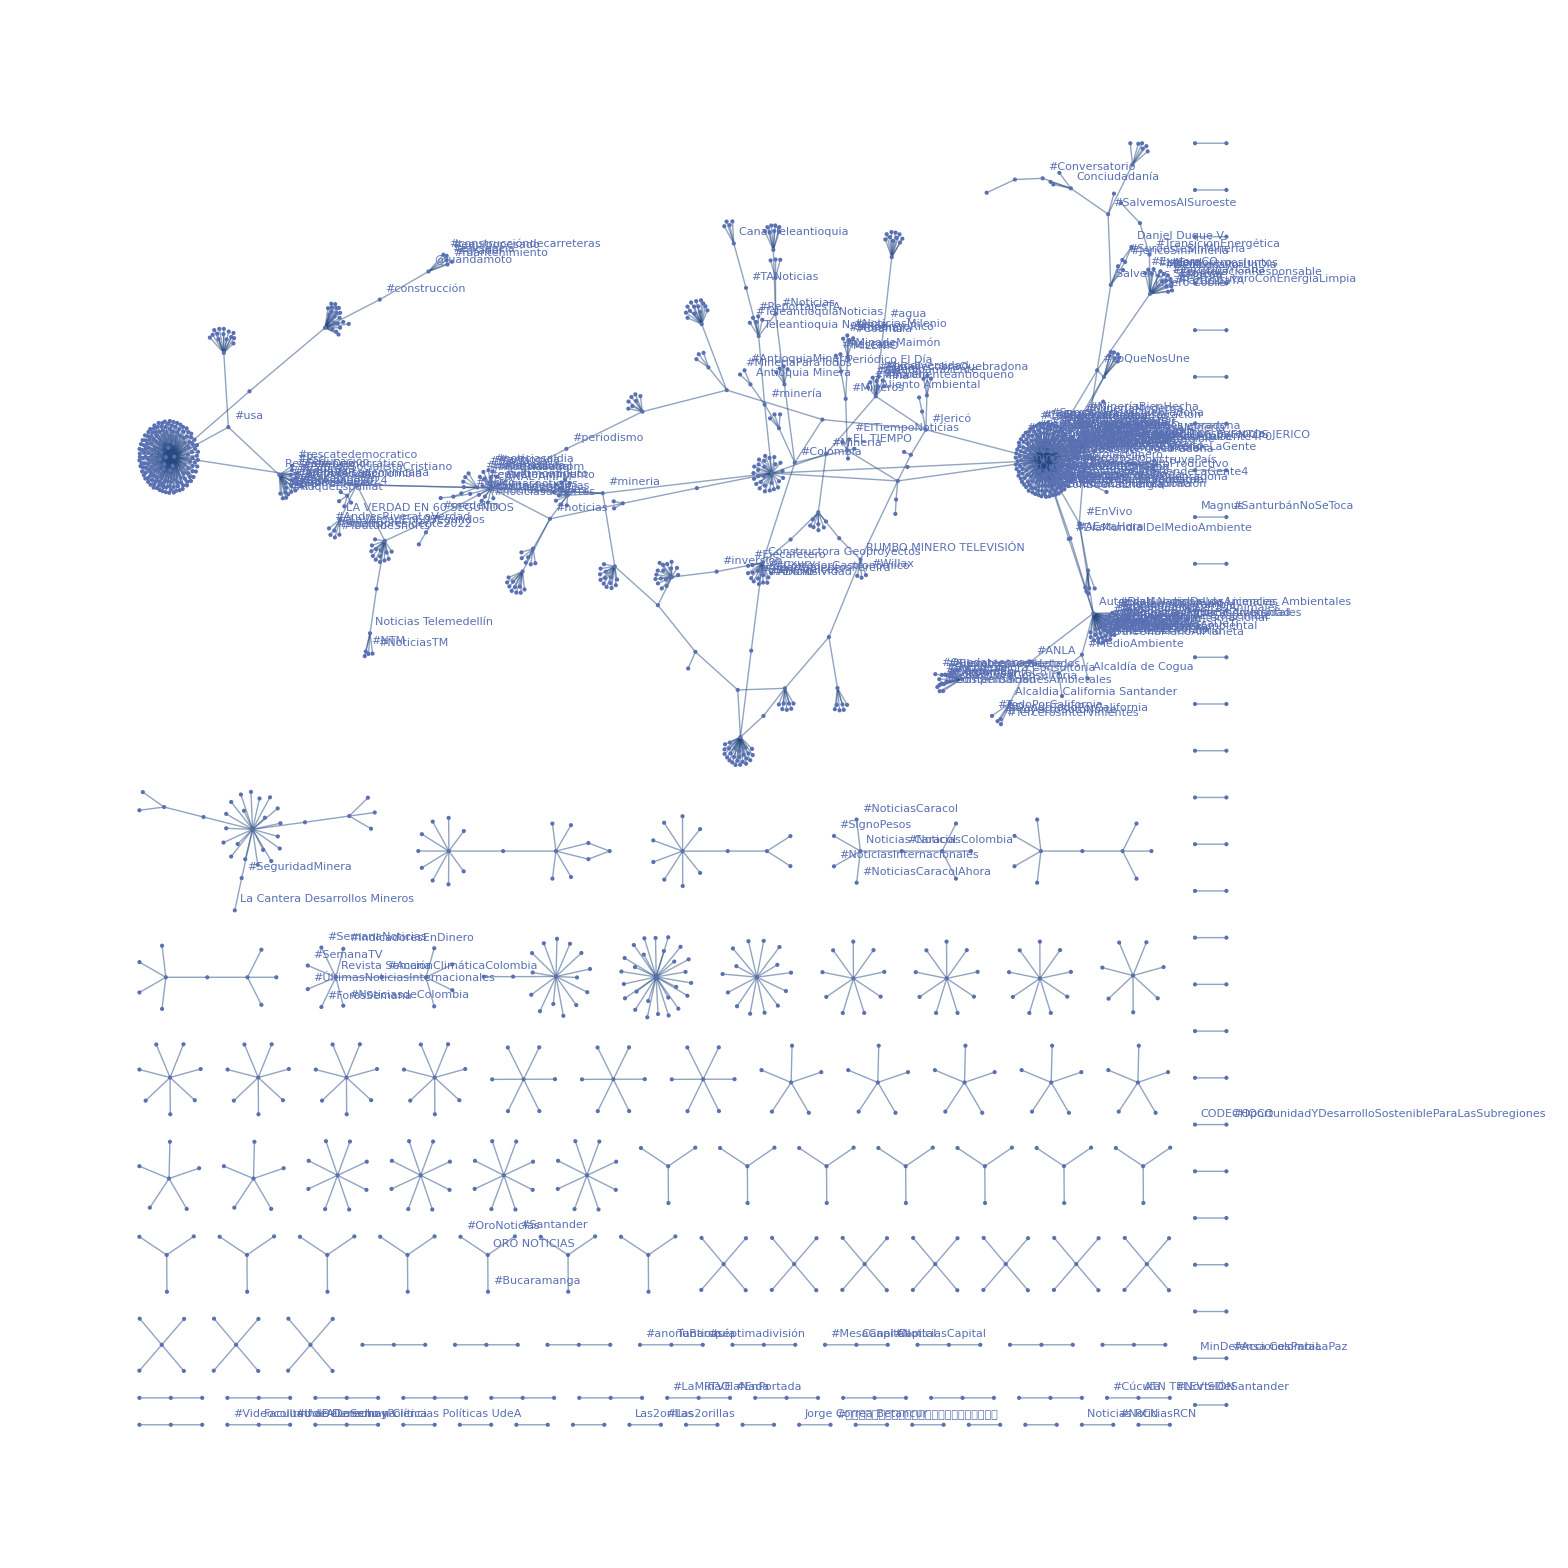

```mathematica
Graph[DeleteDuplicates[Table[NewPositions[[ii,1]]<->NewPositions[[ii,2]],{ii,1,Length[NewPositions]}]],VertexLabels->VrtxLabl,ImageSize->5000]
```

```mathematica
SpecialList=DeleteDuplicates[Select[NewPositions,MemberQ[Select[Tally[NewPositions[[All,1]]],#[[2]]>1&][[All,1]],#[[1]]]&]];
```

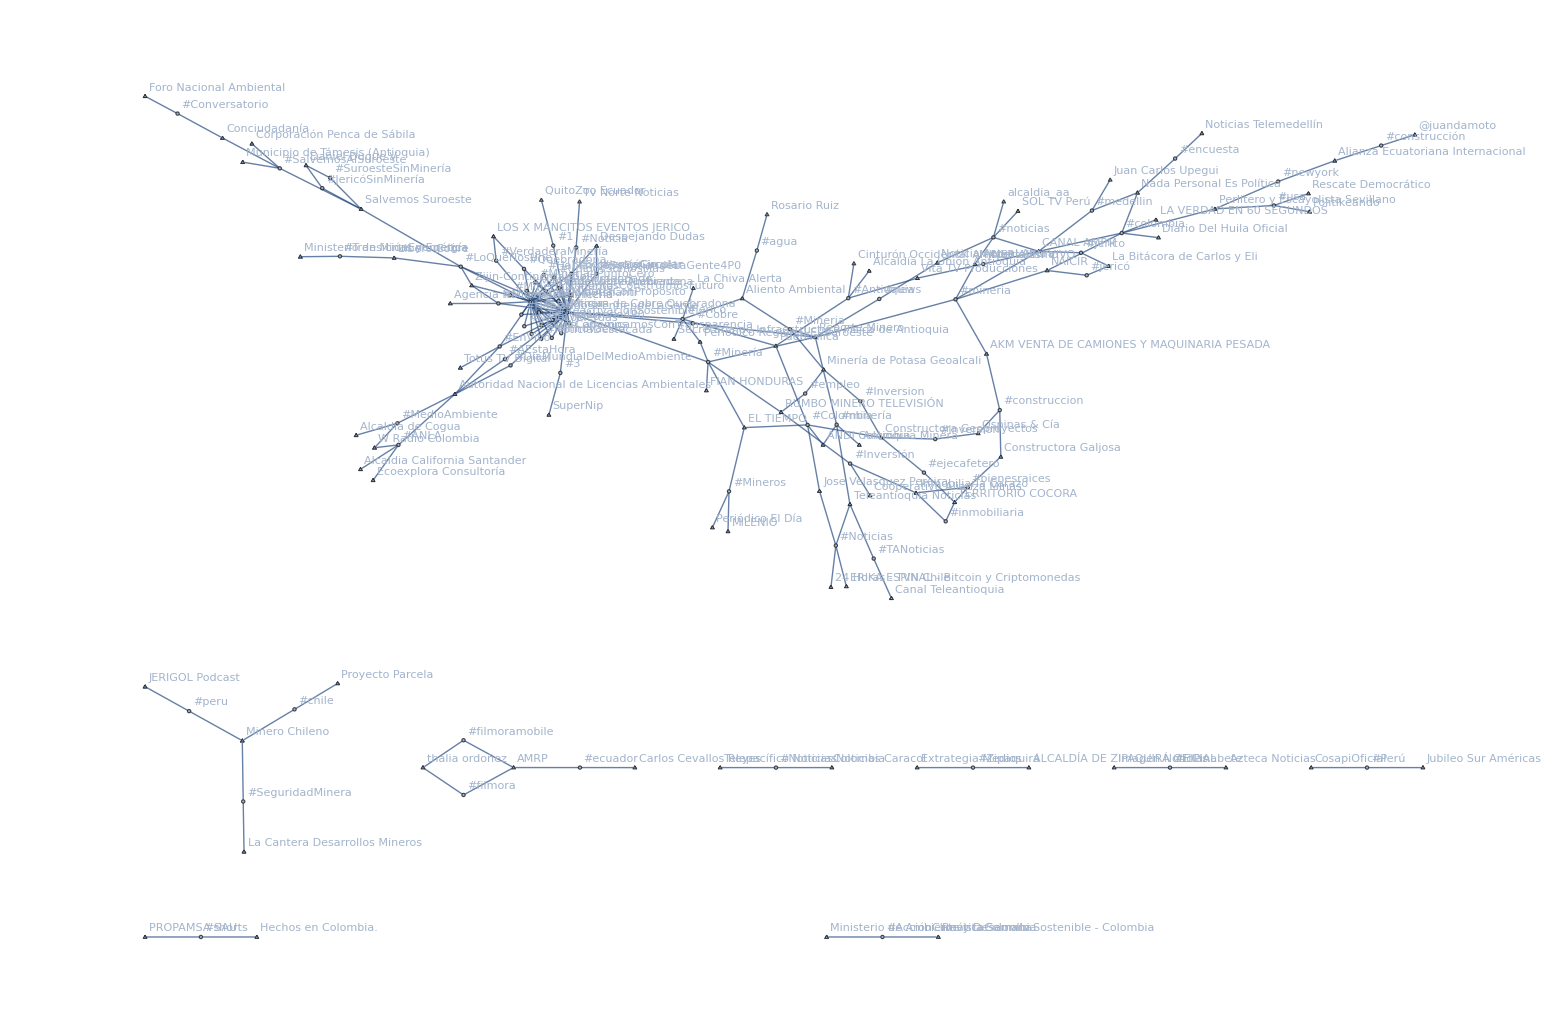

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
NewGraph=Graph[Table[SpecialList[[ii,1]]<->SpecialList[[ii,2]],{ii,1,Length[SpecialList]}],VertexLabels->DeleteDuplicates[Select[VrtxLabl,MemberQ[DeleteDuplicates[Flatten[SpecialList]],#[[1]]]&]],VertexShapeFunction->Select[Table[If[ii<Length[Hashtags],ii->"Circle",ii->"Triangle"],{ii,1,Length[Canales]+Length[Hashtags]}],MemberQ[DeleteDuplicates[Flatten[SpecialList]],#[[1]]]&],VertexSize->0.4,GraphLayout->Automatic,ImageSize->2000]
```

# Tercer Intento

```mathematica
NewData1=Import["C:\\Users\\Administrador\\Downloads\\datos_menciones (1).xlsx"][[1]][[All,{2,3}]];
```

```mathematica
NewData2=DeleteDuplicates[Select[Select[NewData1,Unequal[#,{"",""}]&],Unequal[#[[1]],"@gmail"]&&Unequal[#[[1]],"@s"]&&Unequal[#[[1]],"@esgrum"]&][[2;;]]];
```

```mathematica
NewData2//TableForm
```

@NoticiasCaracol | Noticias Caracol
@camaramedellin | Minera de Cobre Quebradona
@bluradio | Blu Radio
@Teleantioquia | Antioquia Minera
@LaLoqueraProduccionesOficial | Eduardo Garcia S.
@rescate | Rescate Democrático
@AmeliaRueda | AmeliaRueda
@canaltro | Oriente Noticias Canal TRO
@noticiasTRO | Oriente Noticias Canal TRO
@CanalTRO | Oriente Noticias Canal TRO
@GustavoPetroOficial | LA VERDAD EN 60 SEGUNDOS
@mindefensa | MinDefensa Colombia
@policia | Policía Nacional de Colombia
@comfenalcoant | Minera de Cobre Quebradona
@jose_maria_davila_roman | José María Dávila Román
@vahostvgranada | Vahos Tv
@hora13noticias | Hora 13 Noticias
@olca | Comunicaciones OLCA
@clandestinos3232 | Corazón de la Montaña
@UNTelevision | Universidad Nacional de Colombia | @TelevisionUNAL
@UNColombia | Universidad Nacional de Colombia | @TelevisionUNAL
@rtvcnoticias | RTVC Noticias
@BID | Comfama
@lauraisabelriosmarin | MuseoITM
@fcenudea | MuseoITM
@udea | MuseoITM
@usbmed | MuseoITM
@egresados | MuseoITM
@corantioquiaoficial | MuseoITM
@InadehOficial | INADEH OFICIAL
@N03 | Alcaldía de Medellín
@telepacificotv | Telepacífico Noticias
@TPNoticias_ | Telepacífico Noticias
@telepacificonoticias | Telepacífico Noticias
@sinnadaqueocultarrdoficial | SinNadaQueOcultarrd Oficial
@ICBFColombia | Municipio de Támesis (Antioquia)
@FNAmbiental | Foro Nacional Ambiental
@contraloria | ContraloriaColombia
@primarespro | PRIMARES
@Corantioquia | Minera de Cobre Quebradona
@MineradeCobreQuebradona | Minera de Cobre Quebradona
@fundacionjeremiascano | Minera de Cobre Quebradona
@equipoorgullopaisa | Minera de Cobre Quebradona
@yamahamusical | Minera de Cobre Quebradona

```mathematica
Hashtags=NewData2[[All,1]];
Canales=NewData2[[All,2]];
```

```mathematica
NewPositions=Table[{Position[Hashtags,NewData2[[ii,1]]][[1,1]],Position[Canales,NewData2[[ii,2]]][[1,1]]+Length[Hashtags]},{ii,1,Length[NewData2]}];
```

```mathematica
VrtxLabl=DeleteDuplicates[Join[Table[Position[Hashtags,NewData2[[ii,1]]][[1,1]]->NewData2[[ii,1]],{ii,1,Length[NewData2]}],Table[Position[Canales,NewData2[[ii,2]]][[1,1]]+Length[Hashtags]->NewData2[[ii,2]],{ii,1,Length[NewData2]}]]];
```

```mathematica
Length[Hashtags]
```

44

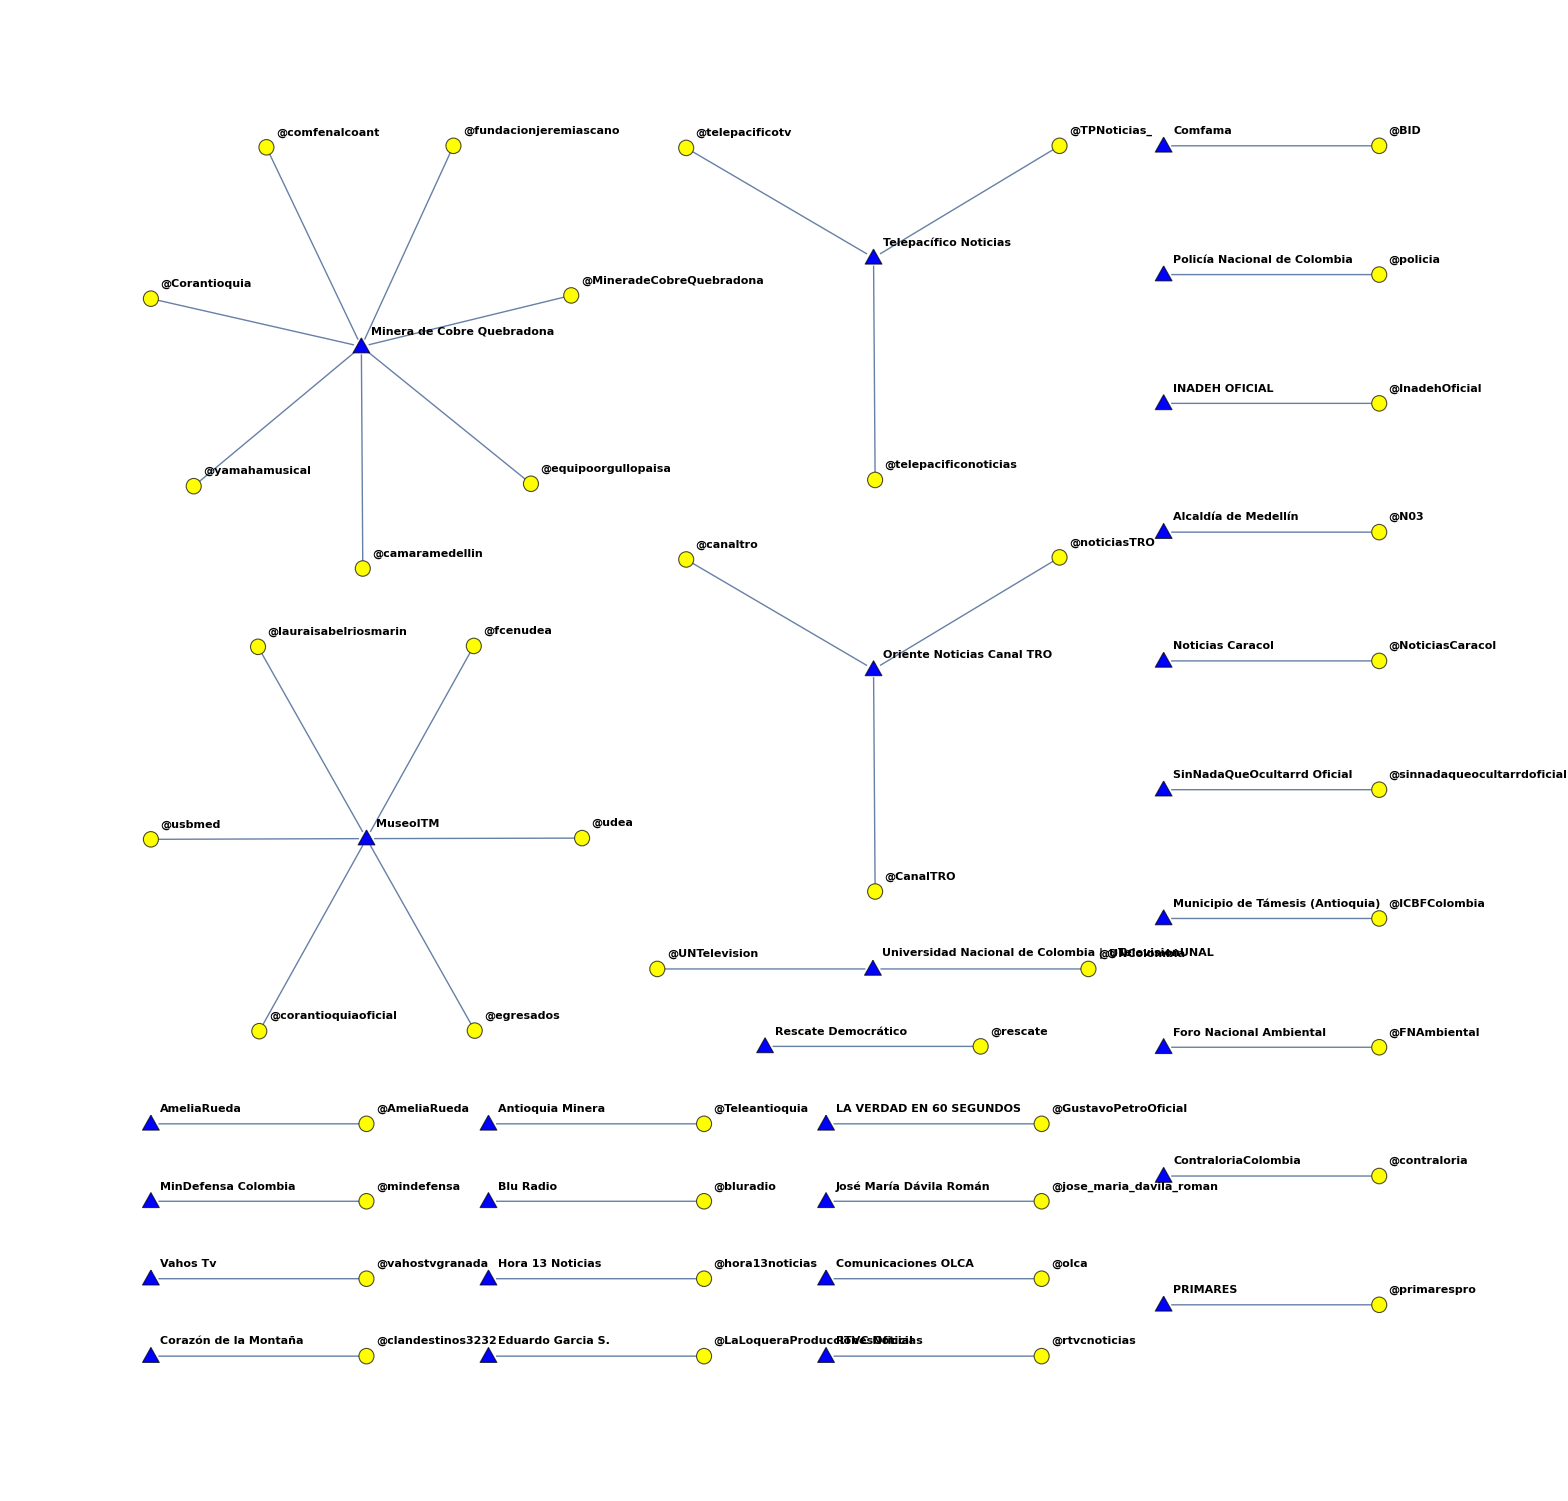

```mathematica
MyGraph=Graph[DeleteDuplicates[Table[NewPositions[[ii,1]]<->NewPositions[[ii,2]],{ii,1,Length[NewPositions]}]],VertexLabels->VrtxLabl,VertexShapeFunction->Select[Table[If[ii<Length[Hashtags]+1,ii->"Circle",ii->"Triangle"],{ii,1,Length[Canales]+Length[Hashtags]}],MemberQ[Flatten[NewPositions],#[[1]]]&],VertexLabelStyle->Directive[Black,Bold],GraphLayout->Automatic,VertexStyle->Select[Table[If[ii<Length[Hashtags]+1,ii->Yellow,ii->Blue],{ii,1,Length[Canales]+Length[Hashtags]}],MemberQ[Flatten[NewPositions],#[[1]]]&],VertexSize->0.2,ImageSize->1780]
```

```mathematica
Export["MyGraph.jpg",MyGraph]
```

MyGraph.jpg

# Cuarto Intento

```mathematica
NewData=Import["C:\\Users\\Administrador\\Downloads\\DATOSHASHTAGS.xlsx"][[1]];
```

```mathematica
Position[NewData[[1]],"FechaPublicacionVideo"]
```

{{7}}

```mathematica
10,6
```

```mathematica
MyData=NewData[[All,{6,7,10}]];
```

```mathematica
MyData1=Select[MyData,Unequal[#[[1]],""]&];
```

```mathematica
MyLists=Gather[MyData1[[2;;]],Equal[#1[[1]],#2[[1]]]&];
```

```mathematica
DateObject[MyLists[[1]][[1]][[2]]]
```

Sat 13 Apr 2019 09:53:24GMT-5

```mathematica
MyLists[[1]][[1]][[2]]
```

2019-04-13T14:53:24Z

```mathematica
NewData=DeleteDuplicates[Import["C:\\Users\\Administrador\\Downloads\\datos_hashtags_emisor_no_repetido_rafa.xlsx"][[1]][[All,{2,3,4}]][[2;;]]];
```

```mathematica
Hashtags=NewData[[All,1]];
Canales=NewData[[All,2]];
```

```mathematica
NewPositions=Table[{Position[Hashtags,NewData[[ii,1]]][[1,1]],Position[Canales,NewData[[ii,2]]][[1,1]]+Length[Hashtags]},{ii,1,Length[NewData]}];
```

```mathematica
VrtxLabl=DeleteDuplicates[Join[Table[Position[Hashtags,NewData[[ii,1]]][[1,1]]->Placed[NewData[[ii,1]],Center],{ii,1,Length[NewData]}],Table[Position[Canales,NewData[[ii,2]]][[1,1]]+Length[Hashtags]->Placed[NewData[[ii,2]],Center],{ii,1,Length[NewData]}]]];
```

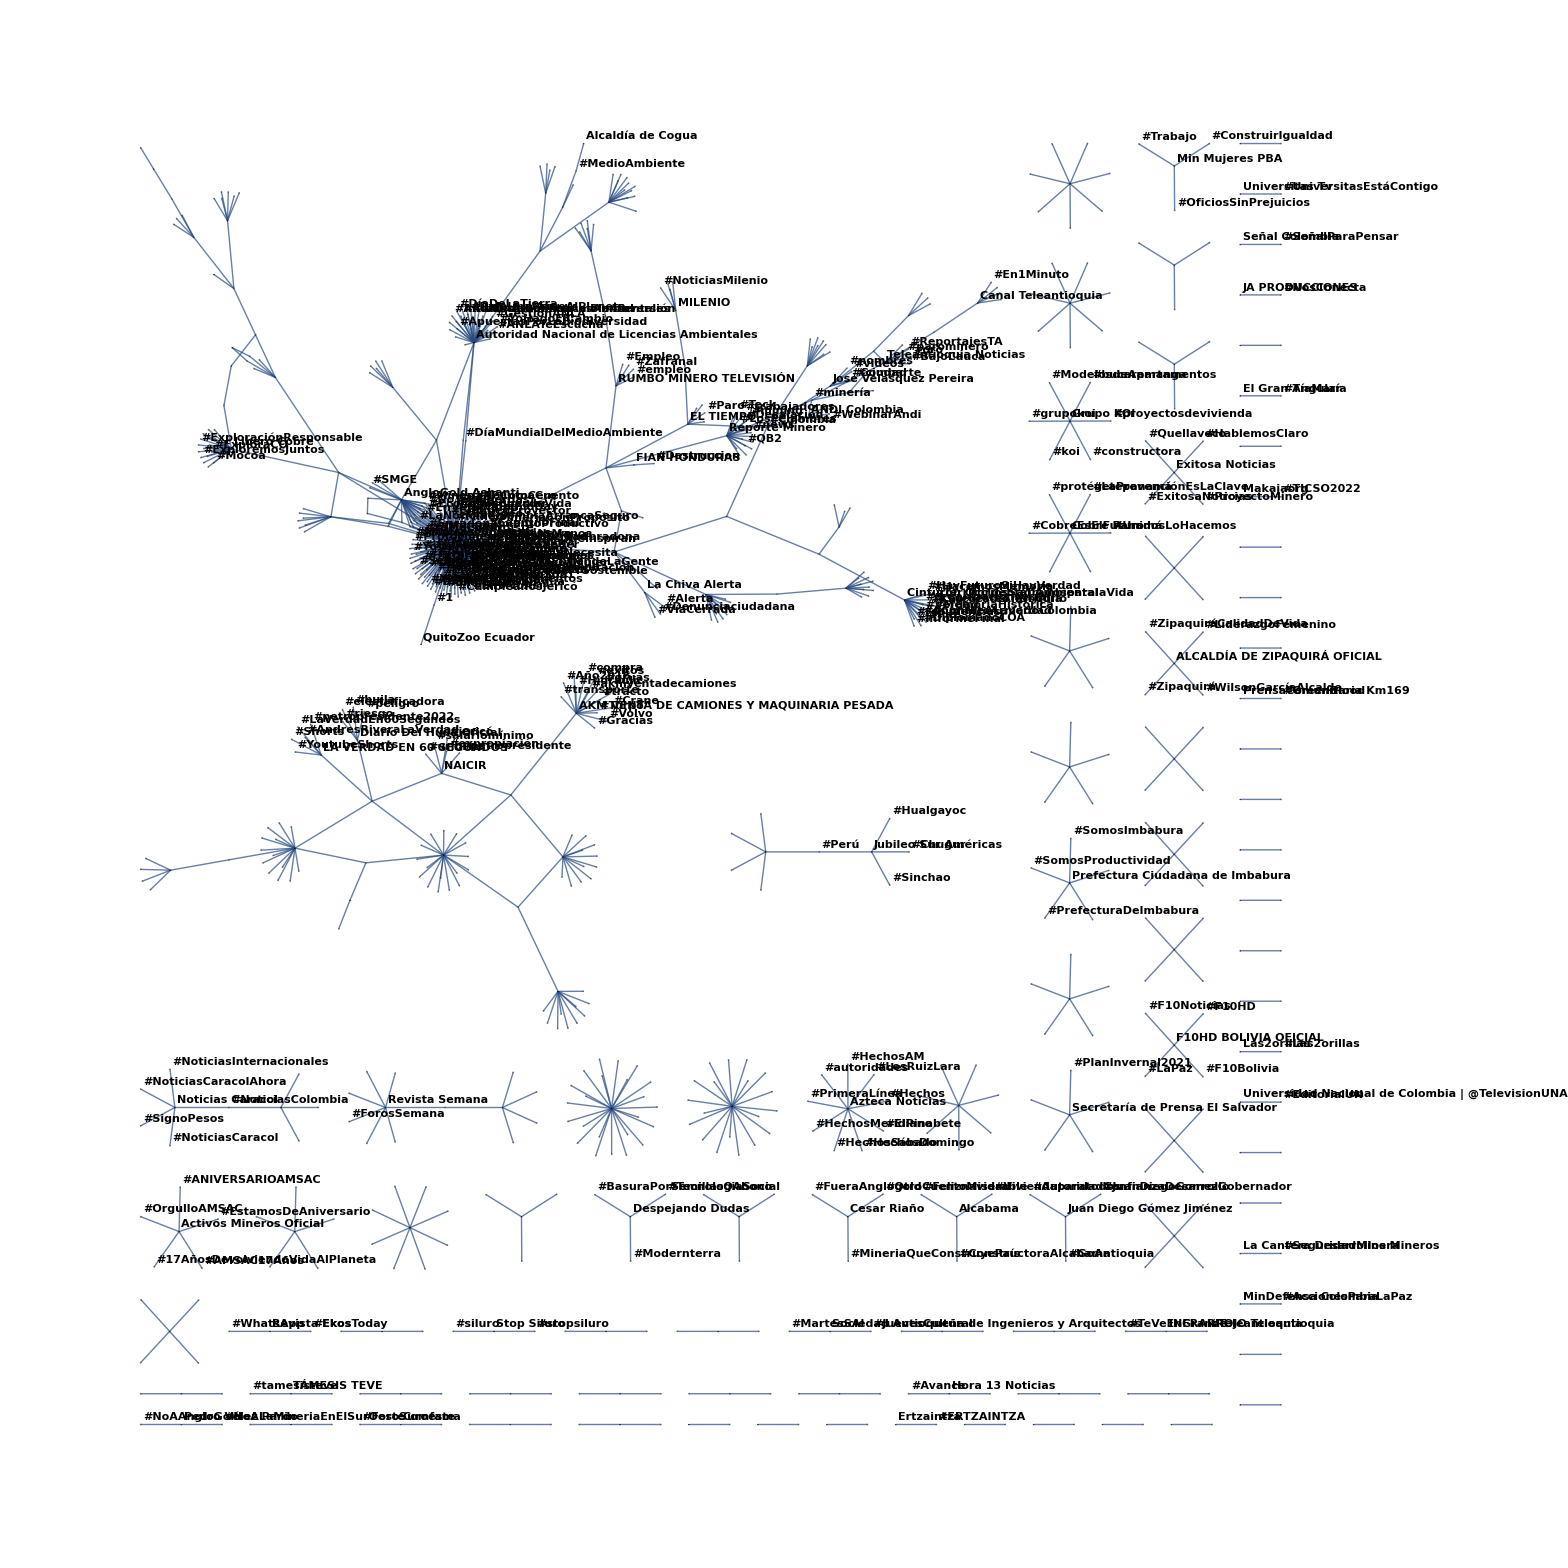

```mathematica
Graph[DeleteDuplicates[Table[NewPositions[[ii,1]]<->NewPositions[[ii,2]],{ii,1,Length[NewPositions]}]],VertexLabels->VrtxLabl,VertexShapeFunction->Select[Table[If[ii<Length[Hashtags]+1,ii->"Circle",ii->"Triangle"],{ii,1,Length[Canales]+Length[Hashtags]}],MemberQ[Flatten[NewPositions],#[[1]]]&],VertexLabelStyle->Directive[Black,Bold],GraphLayout->Automatic,VertexStyle->Select[Table[If[ii<Length[Hashtags]+1,ii->Yellow,ii->Blue],{ii,1,Length[Canales]+Length[Hashtags]}],MemberQ[Flatten[NewPositions],#[[1]]]&],VertexSize->0.2,ImageSize->3000]
```

```mathematica
SpecialList=DeleteDuplicates[Select[NewPositions,MemberQ[Select[Tally[NewPositions[[All,1]]],#[[2]]>1&][[All,1]],#[[1]]]&]];
```

```mathematica
ColorEdge=NewData[[All,3]][[Table[Position[NewPositions,SpecialList[[ii]]][[1,1]],{ii,1,Length[SpecialList]}]]];
```

```mathematica
MyEdgeList=Table[If[Equal[ColorEdge[[ii]],True],Style[SpecialList[[ii,1]]<->SpecialList[[ii,2]],Red],Style[SpecialList[[ii,1]]<->SpecialList[[ii,2]],Black]],{ii,1,Length[SpecialList]}];
```

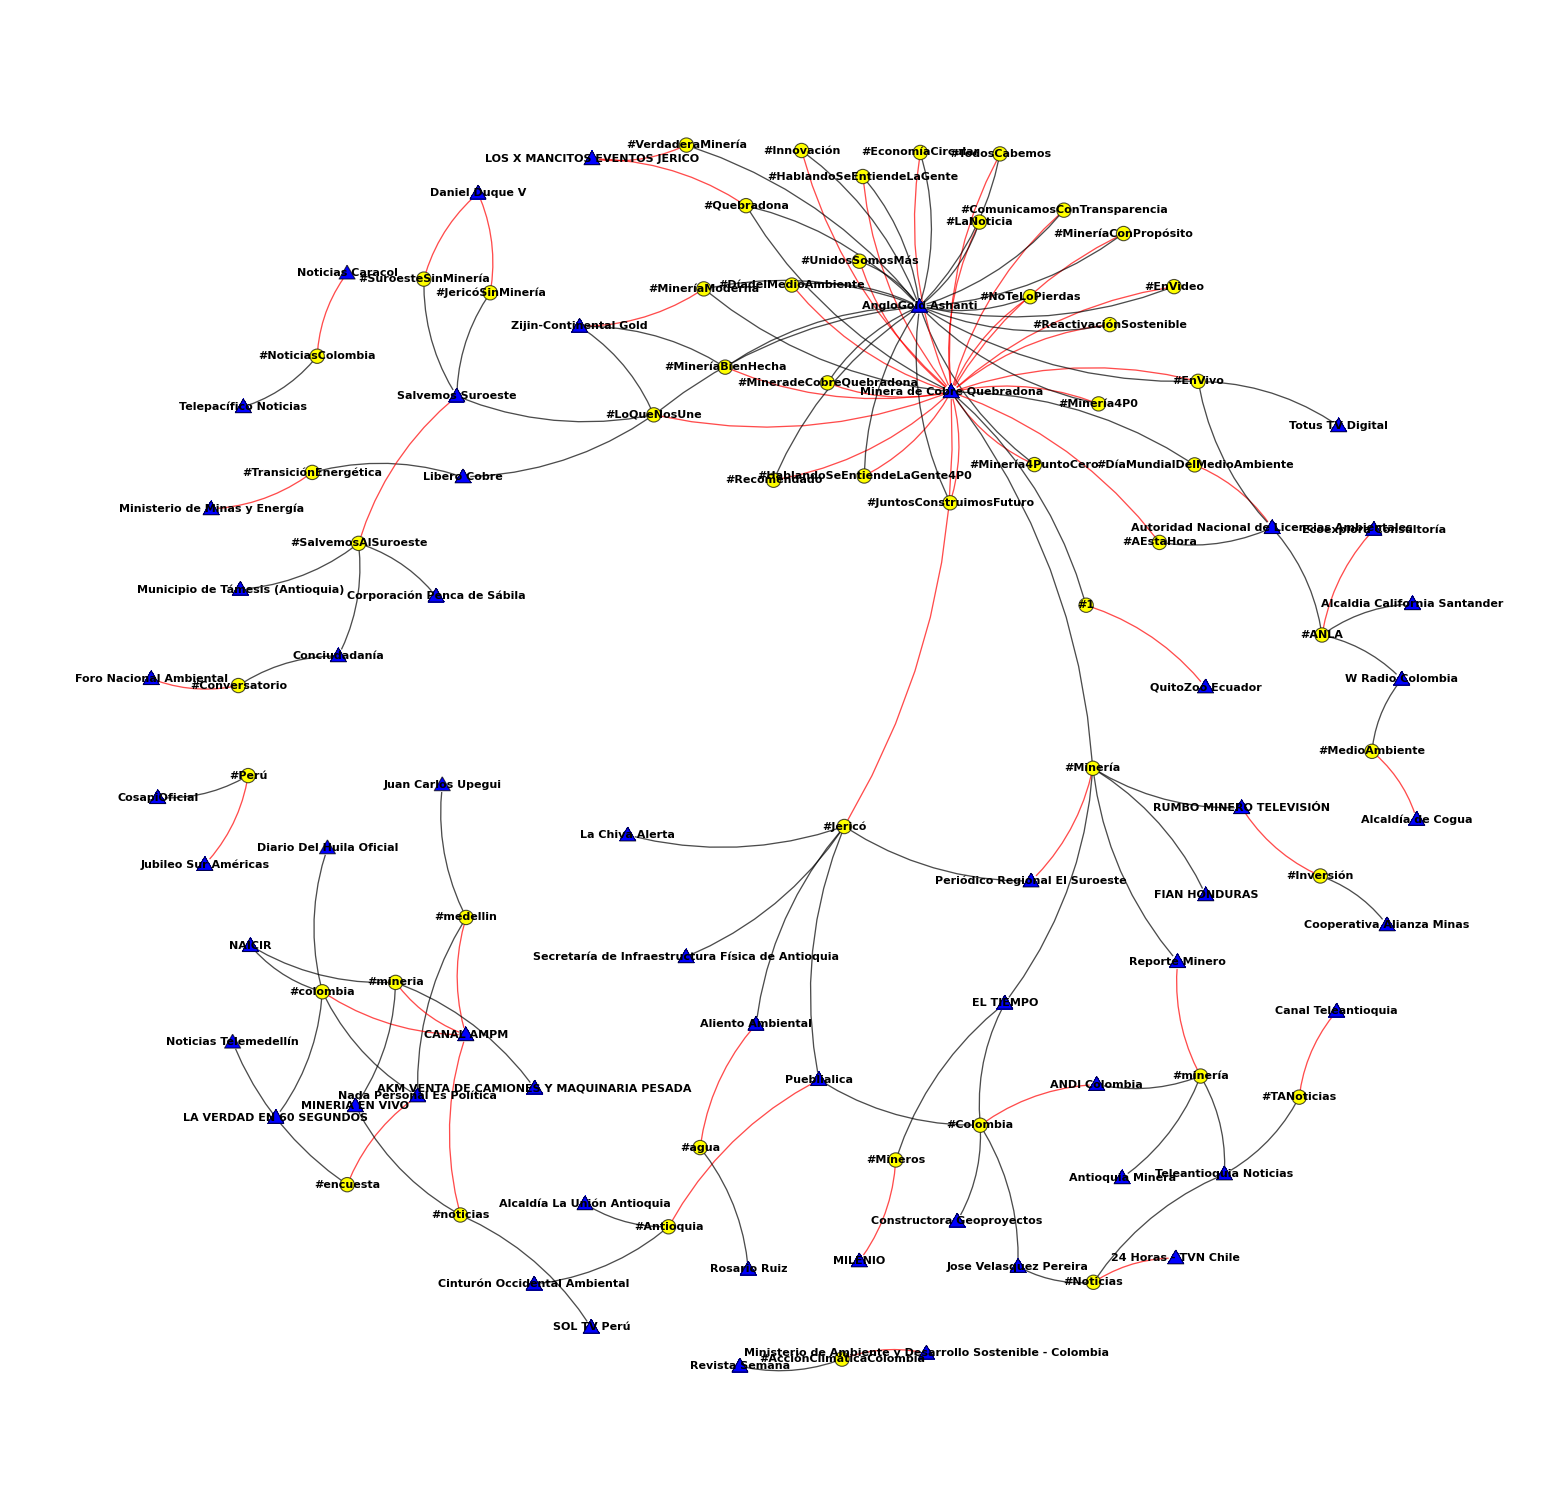

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
NewGraph=Graph[MyEdgeList,VertexLabels->DeleteDuplicates[Select[VrtxLabl,MemberQ[DeleteDuplicates[Flatten[SpecialList]],#[[1]]]&]],VertexShapeFunction->Select[Table[If[ii<Length[Hashtags],ii->"Circle",ii->"Triangle"],{ii,1,Length[Canales]+Length[Hashtags]}],MemberQ[DeleteDuplicates[Flatten[SpecialList]],#[[1]]]&],VertexStyle->Select[Table[If[ii<Length[Hashtags]+1,ii->Yellow,ii->Blue],{ii,1,Length[Canales]+Length[Hashtags]}],MemberQ[Flatten[SpecialList],#[[1]]]&],EdgeStyle->Thickness[0.0006],VertexSize->0.23,VertexLabelStyle->Directive[Black,Bold],GraphLayout->"GravityEmbedding",ImageSize->1700]
```